# Transmission as a process of co-location on a weighted landscape

This notebook shows how co-location on a weighted landscape can be understood as a function of individuals behavioural choices to select a given landscape

## Set up

```mathematica
(*First, some directory stuff for outputting plot*)
baseDir="/Users/colebrookson/github/theRmal-landscape/";
figsDir=FileNameJoin[{baseDir,"figs"}];
relativePath[parts__]:=FileNameJoin[{baseDir,parts}]
```

## Landscape weights

```mathematica
numSimulations = 100000;
nG = 1000;
WgridHomogenous = Table[1/nG, {nG}];  (* note the decimal for machine N *)
Total[WgridHomogenous]
sameLocationCountOneS = 0;
sameLocationCountTwoS = 0;
Do[
  (* Randomly choose cells for S and I *)
  sLocation = RandomChoice[WgridHomogenous -> Range[nG]];
  iLocation = RandomChoice[WgridHomogenous -> Range[nG]];
  
  (* Check if they match *)
  If[sLocation == iLocation, sameLocationCountOneS++];

  (* For two S individuals *)
  sLocations = RandomChoice[WgridHomogenous -> Range[nG], 2];
  iLocation2 = RandomChoice[WgridHomogenous -> Range[nG]];
  
  (* Check if the infected cell matches one of the susceptible cells *)
  If[MemberQ[sLocations, iLocation2], sameLocationCountTwoS++];

	, {numSimulations}
]

(* Calculate proportions *)
proportionSameLocationOneS = sameLocationCountOneS / numSimulations;
proportionSameLocationTwoS = sameLocationCountTwoS / numSimulations;

(* Calculate predicted values based on derivations *)
nS = 1; nI = 1;

epsilon = 1; (* Assume constant epsilon for simplicity *)
predictedProbE = Table[
  epsilon * WgridHomogenous[[i]] * (1 - (1 - WgridHomogenous[[i]])^nS),
  {i, nG}
];
predictedProbAnyE = N[1 - Times @@ (1 - # & /@ predictedProbE)];

(* Print results *)
Print["Proportion of same location for 1 S and 1 I (simulated): ", N[proportionSameLocationOneS]];
Print["Proportion of same location for 2 S and 1 I (simulated): ", N[proportionSameLocationTwoS]];
(*Print["Predicted probability for E at each location: ", predictedProbE];*)
Print["Predicted probability for E occurring at any location: ", predictedProbAnyE];
```

1

Proportion of same location for 1 S and 1 I (simulated): 3.11575

Proportion of same location for 2 S and 1 I (simulated): 0.23343

Predicted probability for E occurring at any location: 0.000999501

## Simulations

Do::iterb: Iterator {r$1775,repsPerKer⟦kerIdx⟧} does not have appropriate bounds.

Do::iterb: Iterator {r$1781,repsPerKer⟦kerIdx⟧} does not have appropriate bounds.

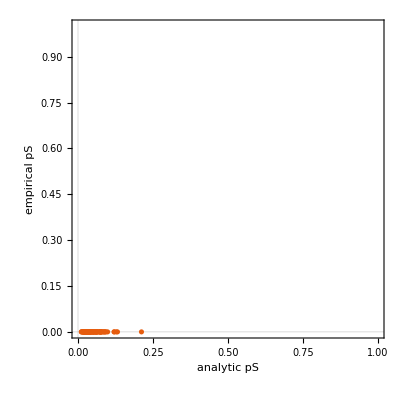

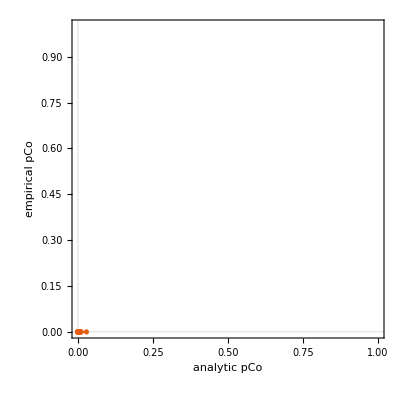

mean abs error pS: 0.0485875

mean abs error pCo: 0.00203378

empirical any co-loc prob: 0.

pred any co-loc prob     : 0.184667

sim same cell (s=1,i=1): 0.

sim same cell (s=2,i=1): 0.

```mathematica
(* ----------------------------------------------------------------------- *)
(* 03  simulation accumulators                                             *)
(* ----------------------------------------------------------------------- *)

doOneOneTest = True;
doTwoOneTest = True;

kernCount   = $KernelCount[];
base        = Quotient[numSim, kernCount];
rem         = Mod[numSim, kernCount];
repsPerKer  = Join[ConstantArray[base + 1, rem],
                   ConstantArray[base, kernCount - rem]];

(* share definitions needed on all kernels *)
DistributeDefinitions[w, n, sCount, iCount, doOneOneTest, doTwoOneTest];


(* ----------------------------------------------------------------------- *)
(* 04  monte carlo loop                                                    *)
(* ----------------------------------------------------------------------- *)

simParts =
  ParallelTable[
    Module[
      {hitCoLocal, anyCoLocal, hitSLocal, hitILocal,
       sameLocOneLocal, sameLocTwoLocal, r},
      
      hitCoLocal     = ConstantArray[0, n];
      hitSLocal      = ConstantArray[0, n];
      hitILocal      = ConstantArray[0, n];
      anyCoLocal     = 0;
      sameLocOneLocal = 0;
      sameLocTwoLocal = 0;
      
      Do[
        (* general draws *)
        sLocs = RandomChoice[w -> Range[n], sCount];
        iLocs = RandomChoice[w -> Range[n], iCount];
        
        (* mark *)
        hitS = ConstantArray[False, n];
        hitI = ConstantArray[False, n];
        hitS[[sLocs]] = True;
        hitI[[iLocs]] = True;
        co = hitS && hitI;
        
        hitSLocal += Boole[hitS];
        hitILocal += Boole[hitI];
        hitCoLocal += Boole[co];
        If[Or @@ co, anyCoLocal++];
        
        (* small special tests *)
        If[doOneOneTest,
          sLoc1 = RandomChoice[w -> Range[n]];
          iLoc1 = RandomChoice[w -> Range[n]];
          If[sLoc1 == iLoc1, sameLocOneLocal++];
        ];
        If[doTwoOneTest,
          sLoc2 = RandomChoice[w -> Range[n], 2];
          iLoc2 = RandomChoice[w -> Range[n]];
          If[MemberQ[sLoc2, iLoc2], sameLocTwoLocal++];
        ];
      ,
      {r, repsPerKer[[kerIdx]]}
      ];
      
      {hitSLocal, hitILocal, hitCoLocal, anyCoLocal,
       sameLocOneLocal, sameLocTwoLocal}
    ],
    {kerIdx, Length[repsPerKer]}
  ];
  
(* ----------------------------------------------------------------------- *)
(* 05  combine results                                                     *)
(* ----------------------------------------------------------------------- *)

hitSCount        = Total[simParts[[All, 1]]];
hitICount        = Total[simParts[[All, 2]]];
hitCoCount       = Total[simParts[[All, 3]]];
anyCoCount       = Total[simParts[[All, 4]]];
sameLocCountOneS = Total[simParts[[All, 5]]];
sameLocCountTwoS = Total[simParts[[All, 6]]];

pSEmp  = N[hitSCount/numSim];
pIEmp  = N[hitICount/numSim];
pCoEmp = N[hitCoCount/numSim];
pAnyEmp = N[anyCoCount/numSim];
propSameLocOneS = N[sameLocCountOneS/numSim];
propSameLocTwoS = N[sameLocCountTwoS/numSim];


(* ----------------------------------------------------------------------- *)
(* 06  plots and errors                                                    *)
(* ----------------------------------------------------------------------- *)

plotIdx = If[n <= plotSample, Range[n],
  RandomSample[Range[n], plotSample]
];

dataPS  = Transpose[{pSAnalytic[[plotIdx]], pSEmp[[plotIdx]]}];
dataPCo = Transpose[{pCoAnalytic[[plotIdx]], pCoEmp[[plotIdx]]}];

plotPS = ListPlot[
  dataPS,
  AxesLabel -> {"analytic pS", "empirical pS"},
  PlotRange -> {{0, 1}, {0, 1}},
  AspectRatio -> 1,
  PlotTheme -> "Scientific"
];

plotPCo = ListPlot[
  dataPCo,
  AxesLabel -> {"analytic pCo", "empirical pCo"},
  PlotRange -> {{0, 1}, {0, 1}},
  AspectRatio -> 1,
  PlotTheme -> "Scientific"
];

plotPS
plotPCo

absErrS  = Mean[Abs[dataPS[[All, 2]] - dataPS[[All, 1]]]];
absErrCo = Mean[Abs[dataPCo[[All, 2]] - dataPCo[[All, 1]]]];

Print["mean abs error pS: ", absErrS];
Print["mean abs error pCo: ", absErrCo];
Print["empirical any co-loc prob: ", pAnyEmp];
Print["pred any co-loc prob     : ", predProbAny];

If[iCount == 1,
  Print["pred any co-loc (i=1)   : ", predProbAnyIeq1];
];

If[doOneOneTest,
  Print["sim same cell (s=1,i=1): ", propSameLocOneS];
];

If[doTwoOneTest,
  Print["sim same cell (s=2,i=1): ", propSameLocTwoS];
];

(* ----------------------------------------------------------------------- *)
(* 07  todo: exporting                                                     *)
(* ----------------------------------------------------------------------- *)

(* TODO: export plots and tables as needed, e.g.: *)
(* Export["pS_scatter.pdf", plotPS]; *)
(* Export["pCo_scatter.pdf", plotPCo]; *)
(* Export["empirical_vs_analytic.csv", ...] *)
```